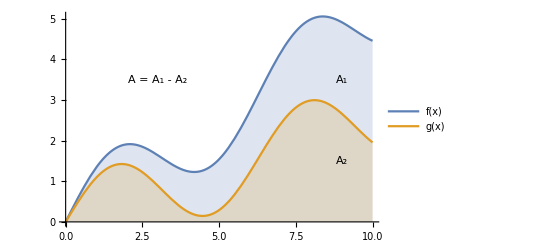

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
picture=Show[
Plot[{Sin[x]+x/2,Sin[x]+x/4},{x,0,10},PlotLegends->{f[x],g[x]},Filling->0],
Graphics@Style[Text["A_1",{9,3.5}],16],
Graphics@Style[Text["A_2",{9,1.5}],16],
Graphics@Style[Text["A = A_1 - A_2",{3,3.5}],16]
]
Export["_assets\\images\\6.1.01.png",picture];
```